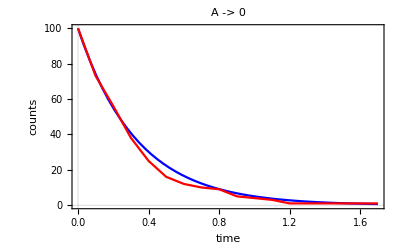

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["../data/A.txt","Table"];

leg=LineLegend[{Blue,Red},{"Theory","Gillespie SSA"},LabelStyle->Directive[FontSize->24]];

plt=Row[{
Show[
Plot[data[[1,2]]*Exp[-3*t],{t,0,data[[-1,1]]},PlotStyle->Blue],
ListLinePlot[data,PlotStyle->Red],
FrameLabel->{"time","counts"},
PlotLabel->"A -> 0"
],leg
}]
```

```mathematica
Export["figure.jpg",plt,ImageResolution->200]
```

figure.jpg